Exercises for Section 19 | Dates and Times

Compute how many days have elapsed since January 1, 1900. |

SAMPLE EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
Now-DateObject[{1900, 1, 1}]
```

44436. days

Compute what day of the week January 1, 2000 was. |

SAMPLE EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
DayName[DateObject[{2000,1,1}]]
```

Saturday

Find the date a hundred thousand days ago. |

SAMPLE EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
Today-Quantity[100000,"Days"]
```

November 15, 1747 12:00 am

Find the local time in Delhi. |

SAMPLE EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
LocalTime[Entity["City",{"Delhi","Delhi","India"}]]
```

August 30, 2021 11:14 pmGMT+5.5

Find the length of daylight today by subtracting today’s sunrise from today’s sunset. |

SAMPLE EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
Sunset[Here,Today]-Sunrise[Here,Today]
```

794 min

Generate an icon for the current phase of the moon. |

SAMPLE EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
MoonPhase[Now,"Icon"]
```

-Graphics-

Make a list of the numerical phase of the moon for each of the next 10 days. |

SAMPLE EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
MoonPhase[{DateRange[Now+1 Quantity[, "Days"],(Now+1 Quantity[, "Days"])+10 Quantity[, "Days"]]}]
```

MoonPhase::dtspec: {{DateObject[{2021,8,31,12,54,20.4115},Instant,Gregorian,-5.],DateObject[{2021,9,1,12,54,20.4115},Instant,Gregorian,-5.],«7»,DateObject[{2021,9,9,12,54,20.4115},Instant,Gregorian,-5.],«1»}} is not a valid date specification.

MoonPhase[{{August 31, 2021 12:54 pmGMT-5,September 1, 2021 12:54 pmGMT-5,September 2, 2021 12:54 pmGMT-5,September 3, 2021 12:54 pmGMT-5,September 4, 2021 12:54 pmGMT-5,September 5, 2021 12:54 pmGMT-5,September 6, 2021 12:54 pmGMT-5,September 7, 2021 12:54 pmGMT-5,September 8, 2021 12:54 pmGMT-5,September 9, 2021 12:54 pmGMT-5,September 10, 2021 12:54 pmGMT-5}}]

```mathematica
Table[MoonPhase[d],{d,Now+1 Quantity[, "Days"],Now+11 Quantity[, "Days"],1 Quantity[, "Days"]}]

Table[MoonPhase[d],{d,Today+1 Quantity[, "Days"],Today+11 Quantity[, "Days"],1 Quantity[, "Days"]}]
```

{0.3657,0.276,0.1932,0.1208,0.06236,0.0219,0.002936,0.008149,0.03878,0.0942,0.1718}

{0.4158,0.3238,0.2369,0.1584,0.09193,0.04131,0.01032,0.002215,0.01907,0.0613,0.1274}

```mathematica
Table[MoonPhase[Today + n 1 Quantity[, "Days"]], {n, 10}]
```

{0.4158,0.3238,0.2369,0.1584,0.09193,0.04131,0.01032,0.002215,0.01907,0.0613}

```mathematica
Table[MoonPhase[d],{d,Today+1 Quantity[, "Days"],Today+10 Quantity[, "Days"],1 Quantity[, "Days"]}]
```

{0.4158,0.3238,0.2369,0.1584,0.09193,0.04131,0.01032,0.002215,0.01907,0.0613}

Generate a list of icons for the moon phases from today until 10 days from now. |

SAMPLE EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
Table[MoonPhase[d,"Icon"],{d,Today+1 LinguisticAssistant,Today+10 Quantity[, "Days"],1 Quantity[, "Days"]}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Compute the time today between sunrise in New York City and in London. |

SAMPLE EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
Sunrise[Entity["City",{"NewYork","NewYork","UnitedStates"}],Today]-Sunrise[Entity["City",{"London","GreaterLondon","UnitedKingdom"}],Today]
```

311 min

Find the air temperature at the Eiffel Tower at noon yesterday. |

SAMPLE EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
AirTemperatureData[Entity["Building","EiffelTower::5h9w8"],DateObject[Yesterday, TimeObject[{12, 0}]]]
AirTemperatureData[Entity["Building","EiffelTower::5h9w8"],DateObject[Yesterday, TimeObject[{12, 0, 0}]]]
```

66.2 °F

66.2 °F

```mathematica
AirTemperatureData[Entity["Building","EiffelTower::5h9w8"],DateObject[Yesterday, TimeObject[{12, 0, 0}]]]
```

66.2 °F

```mathematica
AirTemperatureData[Entity["Building","EiffelTower::5h9w8"],DateObject[Yesterday, TimeObject[{12, 0,0}]]]
```

66.2 °F

Plot the temperature at the Eiffel Tower over the past week. |

SAMPLE EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
DateListPlot[AirTemperatureData[Entity["Building","EiffelTower::5h9w8"],{DatePlus[Today, -Quantity[1, "Weeks"]],Now}]]
```

-Graphics-

Find the difference in air temperatures between Los Angeles and New York City now. |

SAMPLE EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
AirTemperatureData[Entity["City",{"NewYork","NewYork","UnitedStates"}],Now]-AirTemperatureData[Entity["City",{"LosAngeles","California","UnitedStates"}],Now]
```

11.8 °F

```mathematica
AirTemperatureData[Entity["City",{"LosAngeles","California","UnitedStates"}]]
AirTemperatureData[Entity["City",{"LosAngeles","California","UnitedStates"}],Now]
```

71.1 °F

71.1 °F

```mathematica
AirTemperatureData[Entity["City",{"LosAngeles","California","UnitedStates"}]]-AirTemperatureData[Entity["City",{"NewYork","NewYork","UnitedStates"}]]
```

-11.8 °F

Plot the historical frequency of the word “groovy”. |

EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
DateListPlot[WordFrequencyData["groovy","TimeSeries"]]
```

-Graphics-

Compute how many weeks have elapsed since January 1, 1900. |

SAMPLE EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
UnitConvert[Today-DateObject[{1900, 1, 1}],"Weeks"]
```

6348 wk

Compute the time between 3 pm today and sunset today. |

SAMPLE EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
Sunset[Today]-TimeObject[{15,0,0}]
```

Minute: August 30, 2021 6:22 pmGMT-5-15:00:00TimeObject[{15,0,0},Instant,None]

```mathematica
Sunset[Here, Today] - DateObject[Today, TimeObject[{15}]]
```

3 h

```mathematica
Sunset[Today]
Sunset[Here,Today]
```

Minute: August 30, 2021 6:22 pmGMT-5

Minute: August 30, 2021 6:22 pmGMT-5

```mathematica
DateObject[Today]
```

August 30, 2021 12:00 am

```mathematica
TimeObject[{15,0,0}]
TimeObject[{15}]
```

15:00:00TimeObject[{15,0,0},Instant,None]

Hour: 3 pmTimeObject[{15},Hour,None]

```mathematica
Sunset[Here,Today]-DateObject[Today,TimeObject[{15}]]
```

3 h

```mathematica
DateObject[Today,TimeObject[{15}]]
```

Hour beginning: August 30, 2021 3:00 pmGMT-5

```mathematica
UnitConvert[DateObject[Today,TimeObject[Now]]-Sunrise[Here,Today],"PicoSeconds"]
```

3.174×10^16 ps

Generate an icon of the phase of the moon on August 29, 1959. |

SAMPLE EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
MoonPhase[DateObject[{1959, 8, 29}],"Icon"]
```

-Graphics-

Make a line plot of the numerical phase of the moon for each of the next 30 days. |

SAMPLE EXPECTED OUTPUT »

-Graphics- | ×

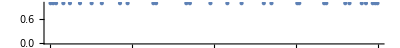

```mathematica
NumberLinePlot[Table[MoonPhase[n],{n,Today+1 Quantity[, "Days"],Today+30 Quantity[, "Days"],1 Quantity[, "Days"]}]]
```

```mathematica
ListLinePlot[Table[MoonPhase[n],{n,Today+1 Quantity[, "Days"],Today+30 Quantity[, "Days"],1 Quantity[, "Days"]}]]
```

-Graphics-

Make a Manipulate of the icon for the moon phase over the next 15 days. |

SAMPLE EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
Manipulate[MoonPhase[n,"Icon"],{n,Today,Today+15 Quantity[, "Days"],1 Quantity[, "Days"]}]
Manipulate[MoonPhase[Today + n Quantity[1, "Days"], "Icon"], {n, 0, 15}]
```

```mathematica
Manipulate[MoonPhase[n,"Icon"],{n,Today,Today+15 Quantity[, "Days"]}]
Manipulate[MoonPhase[Today + n Quantity[, "Days"], "Icon"], {n, 0, 15}];
```

```mathematica
Manipulate[MoonPhase[Today + n *1 Quantity[, "Days"], "Icon"], {n, 0, 15}]
```

```mathematica
Manipulate[MoonPhase[Today+n Quantity[, "Days"],"Icon"],{n,0,15}]
```

Show in a column the times of sunrise for 10 days, starting today. |

SAMPLE EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
Column[Table[Sunrise[Today+n Quantity[, "Days"]],{n,0,9}]]
```

Minute: August 31, 2021 5:09 amGMT-5
Minute: September 1, 2021 5:10 amGMT-5
Minute: September 2, 2021 5:11 amGMT-5
Minute: September 3, 2021 5:12 amGMT-5
Minute: September 4, 2021 5:14 amGMT-5
Minute: September 5, 2021 5:15 amGMT-5
Minute: September 6, 2021 5:16 amGMT-5
Minute: September 7, 2021 5:17 amGMT-5
Minute: September 8, 2021 5:18 amGMT-5
Minute: September 9, 2021 5:19 amGMT-5

Plot together the historical frequencies of the words “science” and “technology”. |

EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
ListLinePlot[WordFrequencyData[{"science","technology"},"TimeSeries"]]
```

-Graphics-